## 代数

## 数列

### 斐波那契数列

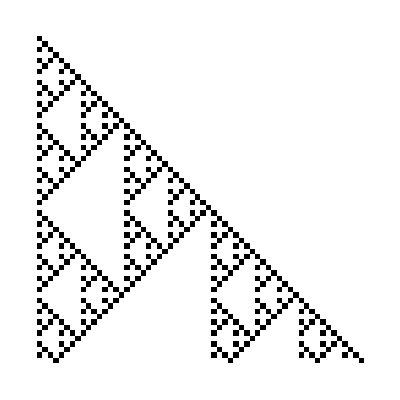

```mathematica
ArrayPlot[Mod[Table[CoefficientList[Fibonacci[n,x],x],{n,60}],2]]
```

黄金螺旋 https://community.wolfram.com/groups/-/m/t/1977738

```mathematica
Manipulate[With[{tf=AffineTransform[{RotationMatrix[-2θ]/GoldenRatio,{1,1}}]},Graphics[{{NestList[tf,RegionBoundary@Rectangle[],n]},Orange,NestList[tf,Circle[(Cot[θ] {1,-1}+1)/2,Csc[θ]/√2,{-θ,θ}+3 π/4],n]},PlotRange->{{-0.1,3},{-0.1,3}},ImageSize->450]],{θ,0.001,π/4},{{n,5},0,9,1}]
```

### 巴都万数列

解析求解

```mathematica
Clear[f]
padovan[n_]=RSolveValue[{f[n+3]==f[n+1]+f[n],f[0]==1,f[1]==1,f[2]==1},f[n],n]//N//Re//Round
```

Round[Re[(0.138938+0.20225 ⅈ) (-0.662359-0.56228 ⅈ)^n+(0.138938-0.20225 ⅈ) (-0.662359+0.56228 ⅈ)^n+0.722124 1.32472^n]]

```mathematica
padovan/@(Range@100-1)//AbsoluteTiming
```

{0.0004844,{1,1,1,2,2,3,4,5,7,9,12,16,21,28,37,49,65,86,114,151,200,265,351,465,616,816,1081,1432,1897,2513,3329,4410,5842,7739,10252,13581,17991,23833,31572,41824,55405,73396,97229,128801,170625,226030,299426,396655,525456,696081,922111,1221537,1618192,2143648,2839729,3761840,4983377,6601569,8745217,11584946,15346786,20330163,26931732,35676949,47261895,62608681,82938844,109870576,145547525,192809420,255418101,338356945,448227521,593775046,786584466,1042002567,1380359512,1828587033,2422362079,3208946545,4250949112,5631308624,7459895657,9882257736,13091204281,17342153393,22973462017,30433357674,40315615410,53406819691,70748973084,93722435101,124155792775,164471408185,217878227876,288627200960,382349636061,506505428836,670976837021,888855064897}}

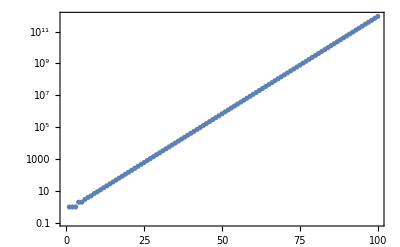

```mathematica
ListLogPlot[Last@%,PlotTheme->"Detailed"]
```

递推

```mathematica
RecurrenceTable[{f[n+3]==f[n+1]+f[n],f[0]==1,f[1]==1,f[2]==1},f,{n,0,99}]//AbsoluteTiming
```

{0.0004018,{1,1,1,2,2,3,4,5,7,9,12,16,21,28,37,49,65,86,114,151,200,265,351,465,616,816,1081,1432,1897,2513,3329,4410,5842,7739,10252,13581,17991,23833,31572,41824,55405,73396,97229,128801,170625,226030,299426,396655,525456,696081,922111,1221537,1618192,2143648,2839729,3761840,4983377,6601569,8745217,11584946,15346786,20330163,26931732,35676949,47261895,62608681,82938844,109870576,145547525,192809420,255418101,338356945,448227521,593775046,786584466,1042002567,1380359512,1828587033,2422362079,3208946545,4250949112,5631308624,7459895657,9882257736,13091204281,17342153393,22973462017,30433357674,40315615410,53406819691,70748973084,93722435101,124155792775,164471408185,217878227876,288627200960,382349636061,506505428836,670976837021,888855064897}}

使用 NestList

```mathematica
Nest[Function[{list},Append[list,list[[-2]]+list[[-3]]]],{1,1,1},97]//AbsoluteTiming
```

{0.0003935,{1,1,1,2,2,3,4,5,7,9,12,16,21,28,37,49,65,86,114,151,200,265,351,465,616,816,1081,1432,1897,2513,3329,4410,5842,7739,10252,13581,17991,23833,31572,41824,55405,73396,97229,128801,170625,226030,299426,396655,525456,696081,922111,1221537,1618192,2143648,2839729,3761840,4983377,6601569,8745217,11584946,15346786,20330163,26931732,35676949,47261895,62608681,82938844,109870576,145547525,192809420,255418101,338356945,448227521,593775046,786584466,1042002567,1380359512,1828587033,2422362079,3208946545,4250949112,5631308624,7459895657,9882257736,13091204281,17342153393,22973462017,30433357674,40315615410,53406819691,70748973084,93722435101,124155792775,164471408185,217878227876,288627200960,382349636061,506505428836,670976837021,888855064897}}

### 雷卡曼数列

```mathematica
Clear[f]
f[0]=0;
f[n_]:=f[n]=If[Or[MemberQ[Last/@Most[DownValues[f]],f[n-1]-n],f[n-1]<n],f[n-1]+n,f[n-1]-n]
```

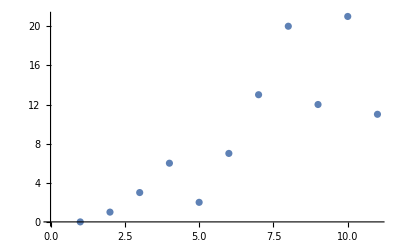
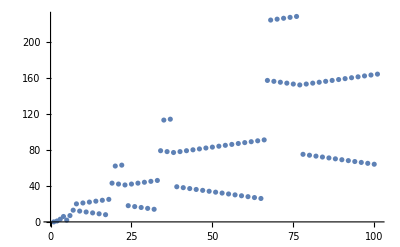
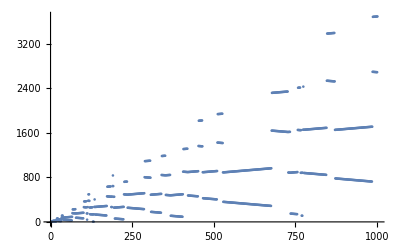

```mathematica
ListPlot[f/@Range[0,#]]&/@{10,100,1000}
```

https://mathematica.stackexchange.com/questions/200882/generate-and-graph-the-recam%c3%a1n-sequence

```mathematica
recamanSequencePlot1=ParametricPlot[Evaluate[Map[RotationTransform[Pi/4]@{Mean@#+(#[[2]]-#[[1]])/2 Cos[t],(#[[2]]-#[[1]])/2 Sin[t]}&,Partition[#,2,1]]],{t,0,-Pi},AspectRatio->Automatic,Axes->False,ImageSize->Large]&;
```

```mathematica
k=30;
list=Table[f[n],{n,0,k}];
recamanSequencePlot1@list
```

```mathematica
recamanSequencePlot2=ParametricPlot[Evaluate[Map[RotationTransform[Pi/4]@{Mean@#+(#[[2]]-#[[1]])/2 Cos[t] r,(#[[2]]-#[[1]])/2 Sin[t] r}&,Partition[#,2,1]]],{t,0,-Pi},{r,0,1},AspectRatio->Automatic,Axes->False,Mesh->None,PlotStyle->Opacity[.2],BoundaryStyle->None]&;

Show[recamanSequencePlot1[list],recamanSequencePlot2[list]]
```

## 函数

### 一元函数

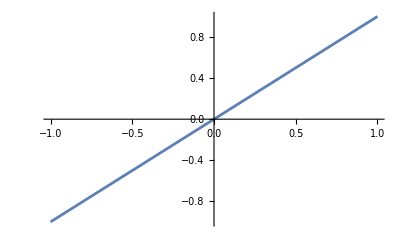
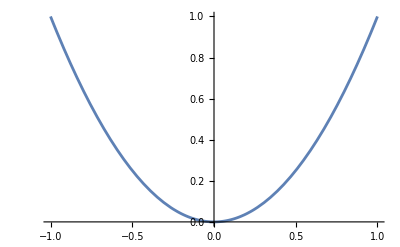
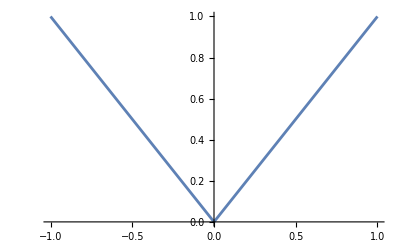
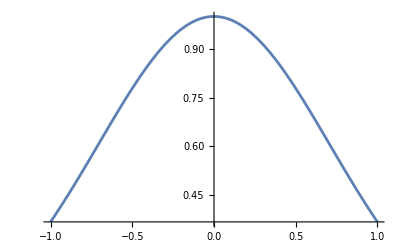
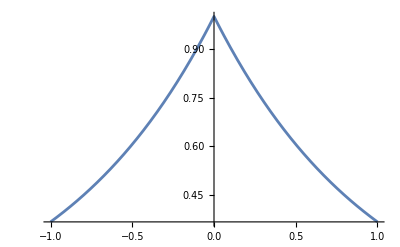
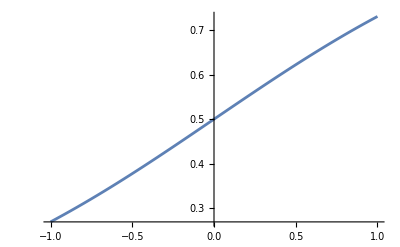

```mathematica
Plot[#,{x,-1,1}]&/@{x,x^2,Abs@x,Exp[-x^2],Exp[-Abs@x],LogisticSigmoid@x}
```

```mathematica
Plot3D[#,{x,-1,1},{y,-1,1}]&/@{x+y,x^2+y^2,Abs@x+Abs@y,Exp[-x^2-y^2],Exp[-Abs@x-Abs@y],LogisticSigmoid[x+y]}
```

### 三元函数

```mathematica
DensityPlot3D[#,{x,-1,1},{y,-1,1},{z,-1,1},ColorFunction->"TemperatureMap"]&/@{x+y+z,x^2+y^2+z^2,Abs@x+Abs@y+Abs@z,Exp[-x^2-y^2-z^2],Exp[-Abs@x-Abs@y-Abs@z],LogisticSigmoid[x+y+z]}
```

```mathematica
ContourPlot3D[#,{x,-1,1},{y,-1,1},{z,-1,1},Contours->10,ColorFunction->"TemperatureMap"]&/@{x+y+z,x^2+y^2+z^2,Abs@x+Abs@y+Abs@z,Exp[-x^2-y^2-z^2],Exp[-Abs@x-Abs@y-Abs@z],LogisticSigmoid[x+y+z]}
```

## 二次型

### 二元二次型

写一个用于可视化二元二次型的函数

```mathematica
QuadraticVisualization2[a_]:=Block[{fun},fun={x,y}.a.{x,y};
{Plot3D[fun,{x,-1,1},{y,-1,1},ColorFunction->"TemperatureMap",PlotTheme->"Minimal"],Show[ContourPlot[fun,{x,-1,1},{y,-1,1},ColorFunction->"TemperatureMap"],VectorPlot[Evaluate@Grad[fun,{x,y}],{x,-1,1},{y,-1,1},VectorColorFunction->None,VectorStyle->Black]]}]
```

正定

```mathematica
QuadraticVisualization2/@{IdentityMatrix[2],{{1,0},{0,2}},{{1.5,.5},{.5,1.5}}}
```

半正定

```mathematica
QuadraticVisualization2/@{{{1,0},{0,0}},{{.5,-.5},{-.5,.5}},{{0,0},{0,1}}}
```

负定

```mathematica
QuadraticVisualization2/@{-IdentityMatrix[2],-{{1,0},{0,2}},-{{1.5,.5},{.5,1.5}}}
```

半负定

```mathematica
QuadraticVisualization2/@{-{{1,0},{0,0}},-{{.5,-.5},{-.5,.5}},-{{0,0},{0,1}}}
```

不定

```mathematica
QuadraticVisualization2/@{{{1,0},{0,-1}},{{-1,0},{0,1}},{{0,1},{1,0}}}
```

### 三元二次型

```mathematica
QuadraticVisualization3[a_]:=Block[{fun},fun={x,y,z}.a.{x,y,z};
{DensityPlot3D[fun,{x,-1,1},{y,-1,1},{z,-1,1},ColorFunction->"TemperatureMap"],ContourPlot3D[fun,{x,-1,1},{y,-1,1},{z,-1,1},ColorFunction->"TemperatureMap",Contours->5],SliceContourPlot3D[fun,"CenterCutBox",{x,-1,1},{y,-1,1},{z,-1,1},ColorFunction->"TemperatureMap"]}
]
```

正定

```mathematica
QuadraticVisualization3/@{IdentityMatrix[3],{{1,0,0},{2,0,0},{3,0,0}},{{1.5,.5,0},{.5,1.5,0},{0,0,1}}}
```

半正定

```mathematica
QuadraticVisualization3/@{DiagonalMatrix[{1,2,0}],DiagonalMatrix[{1,0,2}],{{1,-1,0},{-1,1,0},{0,0,1}},DiagonalMatrix[{1,0,0}]}
```

负定

```mathematica
QuadraticVisualization3/@{-IdentityMatrix[3],-{{1,0,0},{2,0,0},{3,0,0}},-{{1.5,.5,0},{.5,1.5,0},{0,0,1}}}
```

半负定

```mathematica
QuadraticVisualization3/@DiagonalMatrix/@{{-1,-2,0},{0,0,-1}}
```

不定

```mathematica
QuadraticVisualization3/@{DiagonalMatrix[{1,1,-1}],DiagonalMatrix[{1,0,-1}],{{0,1,0},{1,0,0},{0,0,1}}}
```

## 隐函数

直线

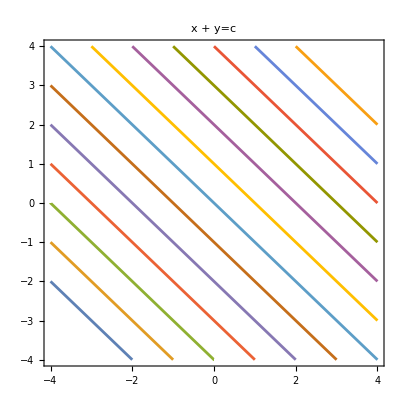
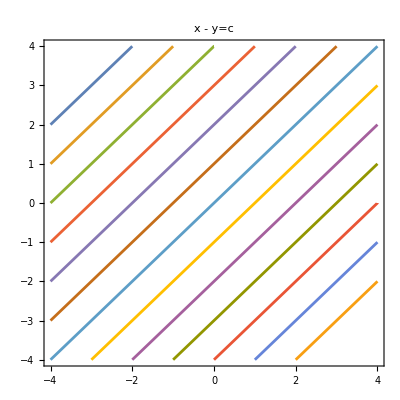
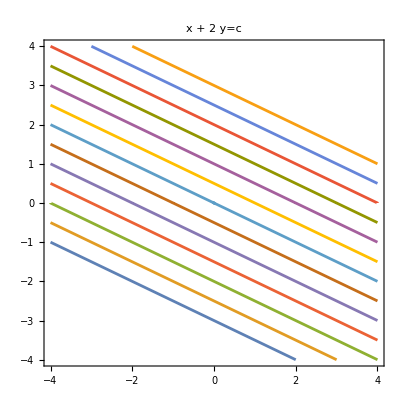
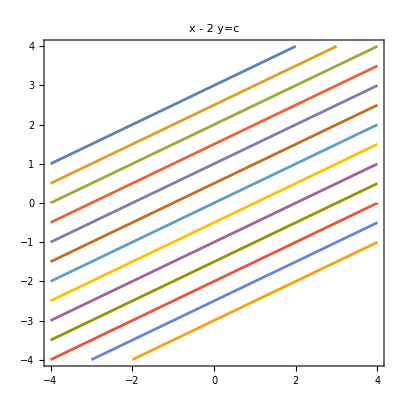
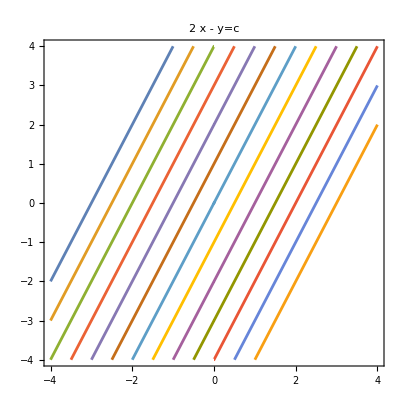
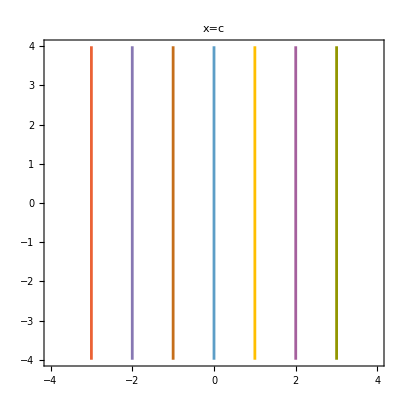
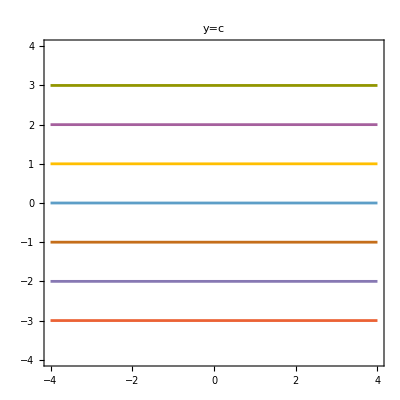

```mathematica
ContourPlot[Evaluate@Table[#==i,{i,-6,6}],{x,-4,4},{y,-4,4},PlotLabel->ToString@#<>"=c"]&/@{x+y,x-y,x+2y,x-2y,2x-y,x,y}
```

抛物线

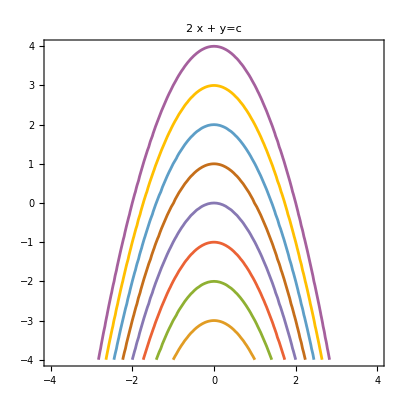
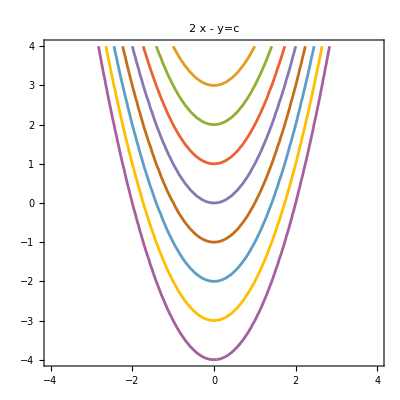
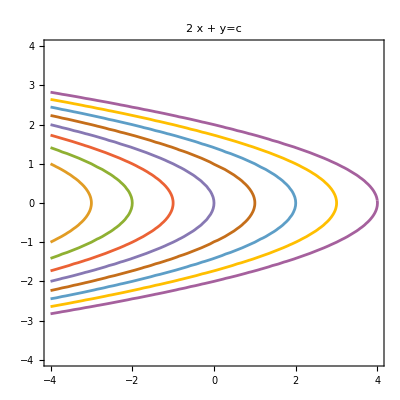
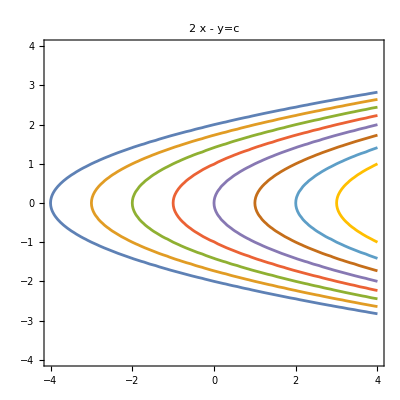

```mathematica
ContourPlot[Evaluate@Table[#==i,{i,-4,4}],{x,-4,4},{y,-4,4},PlotLabel->ToString@#<>"=c"]&/@{x^2+y,x^2-y,x+y^2,x-y^2}
```

## 参数方程

心形线

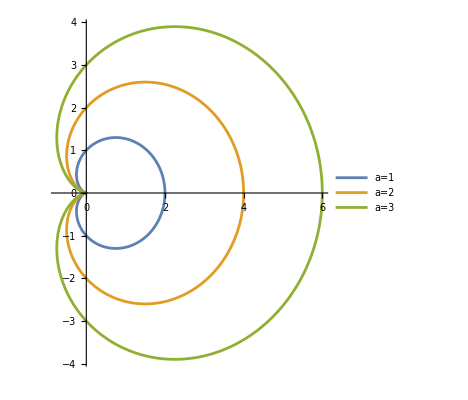

```mathematica
PolarPlot[{1+Cos[θ],2 (1+Cos[θ]),3 (1+Cos[θ])},{θ,0,2 Pi},PlotLegends->{"a=1","a=2","a=3"}]
```

利萨茹曲线

```mathematica
GraphicsGrid@Table[ParametricPlot[{Sin[m u],Sin[n u]},{u,0,2 Pi},PlotTheme->"Minimal"],{n,9},{m,9}]
```

-Graphics-

```mathematica
GraphicsGrid@Table[ParametricPlot[{Sin[m u],Cos[n u]},{u,0,2 Pi},PlotTheme->"Minimal"],{n,9},{m,9}]
```

-Graphics-

球坐标系

```mathematica
SphericalPlot3D[#,{θ,0,Pi},{ϕ,0,2 Pi}]&/@{1,ϕ,θ,1+Sin[5 ϕ] Sin[10 θ]/10}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

圆环（参数方程版本）

```mathematica
ParametricPlot3D[{(2+Cos[v]) Cos[u],(2+Cos[v]) Sin[u],Sin[v]},{u,0,2 Pi},{v,0,2 Pi},Mesh->5,BoundaryStyle->Black,PlotStyle->FaceForm[Red,Yellow]]
```

-Graphics3D-

圆环（旋转曲面版本）

```mathematica
RevolutionPlot3D[{2+Cos[t],Sin[t]},{t,0,2 Pi}]
```

-Graphics3D-

模拟击鼓

```mathematica
Table[RevolutionPlot3D[Cos[(π i)/10] BesselJ[0,t],{t,0,10},PlotRange->{All,All,{-1,1}},Boxed->False,Axes->False,Mesh->None],{i,1,8}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

## 复数

```mathematica
ComplexVisualization[fun_]:={ComplexPlot[fun,{z,-2-2I,2+2I},Mesh->{Range[-5,5,.2],Range[-5,5,.2]},MeshFunctions->{Abs[#2]&,Arg[#2]&},MeshStyle->{White,Black}],ComplexPlot[fun,{z,-2-2I,2+2I},Mesh->{Range[-10,10,.5],Range[-10,10,.5]},MeshFunctions->{Re[#2]&,Im[#2]&},MeshStyle->{White,Black}]}
```

```mathematica
ComplexVisualization/@{z Exp[Pi/6 I],z Exp[Pi/3 I],z Exp[3Pi/4 I]}
```

```mathematica
ComplexVisualization/@{z^2,z^3,z^3+z^2+1}
```

```mathematica
ComplexVisualization/@{1/z,1/(1-z),(z^2-1)/z}
```

```mathematica
ComplexVisualization/@{1/(z^2-1),1/(z^4+1),z/(z^2+z+1)}
```

```mathematica
ComplexVisualization/@{Sqrt[z+1],Sqrt[z^2+1],1/Sqrt[z^3+1]}
```

```mathematica
ComplexVisualization/@{Sin@z,Sin[1/z],z Sin[1/z]}
```

```mathematica
ComplexVisualization/@{z^z,(1/z)^z,z^(1/z)}
```

General::munfl: (0.00441942-3.53103×10^-19 ⅈ)^(226.274+1.80789×10^-14 ⅈ) 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::munfl: (0.000385286-3.31034×10^-19 ⅈ)^(2595.47+2.23001×10^-12 ⅈ) 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::munfl: (0.000133153-3.29655×10^-19 ⅈ)^(7510.17+1.85934×10^-11 ⅈ) 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::stop: 在本次计算中，General::munfl 的进一步输出将被抑制.

```mathematica
ComplexVisualization/@{Exp[z],Exp[-z^2],Exp[1/z]}
```

General::munfl: Exp[-942.431-4.68385×10^-10 ⅈ] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::munfl: Exp[-2.25708×10^7-0.268656 ⅈ] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

```mathematica
ComplexVisualization/@{Log@z,Log[z^2-1],Log[z^4+1]}
```